# NROpsDD for recent experiments - Example Code

Version 1.0 - 03/03/2017

Some caveats for using this code:
	1) There is a slight mistake in the statistical procedure of arXiv:1307.5955 (although it doesn’t make too much difference for the old LUX results). Because of this, we use a different definition of the Test Statistic TS. In our case, TS is the natural log of the Poisson p-value (i.e. the probability of obtaining fewer than the observed number of events for a given mx and λ. For a 90% limit, set TS = Log[0.1] and for a 95% limit set TS = Log[0.05].
	2) Conversion factors are provided for the following operators:  {1, 3, 4, 5, 6, 7, 8, 9, 10, 11}.
	3) The LZ conversion factors (YLZ) are not quite complete - in particular, no interference terms are included, and only contact interactions are allowed. This should be fixed in a future version.

Version 1.1 - 09/06/2017

Currently in the process of checking and updating the calculations. In particular, the test statistic for Xenon1T has now been added, but the conversion factors are not yet available.

## Load the code

Load in the LUX files:

```mathematica
NotebookEvaluate[NotebookDirectory[] <> "LUX/LUX-TS.nb"];
```

Load in the LZ files:

```mathematica
NotebookEvaluate[NotebookDirectory[] <> "LZ/LZ-TS.nb"];
```

These give access to the following functions:
	TSLUX[Log10[mx], Log10[λ]] and YLUX[type][i][N1, N2][mx]
	TSLZ[Log10[mx], Log10[λ]] and YLZ[i][N1, N2][mx]
	
Note that in the case of the LUX conversion factors (Y), we have to specify the “type” of operator, which can be “Contact” or “Long-Range”. In the case of LZ, only the Contact-type operators are implemented (right now), so no need to specify.

Load in the Xe1T files:

```mathematica
NotebookEvaluate[NotebookDirectory[] <> "XENON1T/Xe1T-TS.nb"];
```

This give access to the following function:
	TSXe1T[Log10[mx], Log10[λ]]

## Examples

In the examples below, to change the experiment from LUX to LZ (or vice versa), just replace TSLUX with TSLZ and YLUX with YLZ (noting that in the case of YLZ, you don’t need to specify the “type”).

Note that these examples have been copied (largely) from the NROpsDD website - http://www.marcocirelli.net/NROpsDD.html. See arXiv:1307.5955 for the general philosophy.

### Standard Spin Independent (SI) interaction (LUX WS2014-16)

Effective Operator for SI interaction: 𝒪_1^N=χ̄ χ N̄ N

In non-relativistic expansion the interaction amplitude is <𝒪_1^N> =λ_SI c_1^N 𝒪_1^NR
where
	c_1^N=4m_χ m_N for both proton and neutron
	m_N = nucleon mass in GeV

```mathematica
mN=0.9389;
c["SI Interaction"][N_][mχ_]:=4 mχ mN
```

Benchmark coupling constant (λ_B) as a function of the DM-nucleon SI coupling constant (λ_SI) and the DM mass

λ_B =  λ_SI√(∑ _(N, N' = p, n) c_1^N c_1^N' 𝒴_(1, 1)^(N, N')(m_χ))		 (see the paper for further details)

```mathematica
λB["SI Interaction"][λSI_,mχ_]:=λSI√Sum[c["SI Interaction"][N1][mχ] c["SI Interaction"][N2][mχ] YLUX["Contact"][1,1][N1,N2][mχ],{N1,{"p","n"}},{N2,{"p","n"}}]
```

The DM-nucleon SI Cross Section as a function λ_SI is given by:
σ_p^SI = (λ_SI)^2 μ_χN^2 / π	⇒	λ_SI(σ_p^SI , m_χ) = √(π σ_p^SI / μ_χN^2)
where
	μ_χN= m_χ m_N/ (m_χ+m_N) is the DM-nucleon reduced mass

```mathematica
GeV2cm=1.97 10^-14;(* GeV to cm^-1 conversion factor *)
μ[mχ_,mN]:=mχ mN/(mχ+mN);
λSI["SI Interaction"][σSI_,mχ_]:=√(π σSI/(μ[mχ,mN]GeV2cm)^2)
```

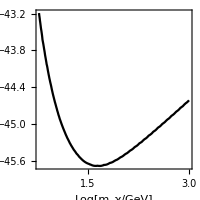

```mathematica
Block[{interaction="SI Interaction"},ContourPlot[TSLUX[lmχ,Log10[λB[interaction][λSI[interaction][10^lσ,10^lmχ],10^lmχ]]]==Log[0.1],
{lmχ,Log10[6],3},{lσ,-47,-40},
ContourStyle->Black,ImageSize->200,PlotRange->All,
FrameLabel->{"Log[m_χ/GeV]","TraditionalForm`LUX"}, PlotLegends->Automatic]]
```

### Standard Spin Dependent (SD) interaction with protons (LZ)

Effective Operator for SD interaction:  𝒪_8^p=χ̄ γ^μ γ^5 χ  p̄ γ_μ γ^5 p

In non-relativistic expansion the interaction amplitude is <𝒪_8^p> =λ_SD^p c_4^p 𝒪_4^NR
where
	c_4^p=-16 m_χ m_N
	m_N = nucleon mass in GeV

```mathematica
mN=0.9389;
c["DM-p SD Interaction"][N_][mχ_]:=-16 mχ mN
```

Benchmark coupling constant (λ_B) as a function of the DM-proton SD coupling constant (λ_SD^p) and the DM mass

λ_B =  λ_SD^p √(c_4^p c_4^p 𝒴_(4, 4)^(p, p)(m_χ))		 (see the paper for further details)

```mathematica
λB["DM-p SD Interaction"][λSD_,mχ_]:=λSD√((c["DM-p SD Interaction"]["p"][mχ])^2 YLZ[4,4]["p","p"][mχ])
```

The DM-proton SD Cross Section as a function of λ_SD is given by:
σ_p^SD = 3 (λ_SD^p)^2 μ_χN^2 / π	⇒	λ_SD^p(σ_p^SD , m_χ) = √(π σ_p^SD /(3 μ_χN^2))
where
	μ_χN= m_χ m_N/ (m_χ+m_N) is the DM-nucleon reduced mass

```mathematica
GeV2cm=1.97 10^-14;(* GeV to cm^-1 conversion factor *)
μ[mχ_,mN]:=mχ mN/(mχ+mN);
λSD["DM-p SD Interaction"][σSD_,mχ_]:=√(π σSD/(3 μ[mχ,mN]^2 GeV2cm^2))
```

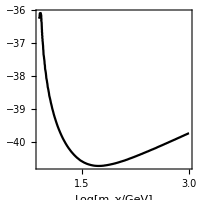

```mathematica
Block[{interaction="DM-p SD Interaction"},ContourPlot[TSLZ[lmχ,Log10[λB[interaction][λSD[interaction][10^lσ,10^lmχ],10^lmχ]]]==Log[0.1],{lmχ,Log10[6],3},{lσ,-43,-33},
ContourStyle->Black,ImageSize->200,PlotRange->All,
FrameLabel->{"Log[m_χ/GeV]","TraditionalForm`LZ"}]]
```